# Analyzing Computational Articles on Wikipedia

## Goal

This project is designed to collect as much information on a specific set of Wikipedia articles as possible. For our set, we will look solely at articles that fall under the category of “Computational _” where “_” represents some field of study.

## Gathering the Data

First, we need to generate a list of titles that fall into this Computational category.

```mathematica
searchlink = "https://en.wikipedia.org/w/index.php?title=Special:Search&limit=500&offset=0&profile=default&search=computational&searchToken=b9fbzhit5sdhvvts5aa00u74l";
xmlResults = Import[searchlink, "XMLObject"];
articles = Union[Flatten[Cases[xmlResults,XMLElement[_,{_,_,
	"title"->str_String/;
		((StringMatchQ[str,StartOfString~~"Computational"~~__])
			&&!(StringContainsQ[str,"Journal",IgnoreCase->True])),_},_]->{str},Infinity]]];
```

The URL for the search was generated by using an Internet browser to search for the 500 top search results of “Computational”. We will then import this as an “XMLObject” where we extract just the titles of the search results. We will filter out any articles that don’t begin with “Computational” as well as articles that contain the substring “Journal” (not case sensitive). This provides us with a list of practically every Computational _ article on Wikipedia. Now we need the data.

```mathematica
TitleToInfo[articleTitle_String]:=
	AssociationMap[WikipediaData[articleTitle, #]&,
		{"ArticlePlaintext", "ExternalLinks", "ArticleContributors", "PageID",
			"SummaryPlaintext", "LanguagesList", "LinksList", "BacklinksList"}];
```

This function takes a title and adds it to an association where its value is another association with the listed fields.

```mathematica
compData = AssociationMap[TitleToInfo, articles];
```

This is a good thing to DumpSave so that excess queries can be avoided.

## Basic Link Analysis

We will now take our list of articles and make an association where each one is a key with its corresponding information. From here, we will look at link analysis.

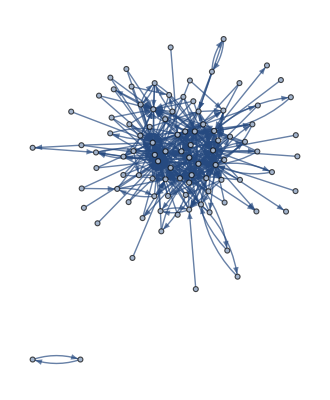

```mathematica
edgeSet = Flatten@Map[Thread, Normal@compData[[;;, "LinksList"]]];
theGraph = Graph[edgeSet];
verticesToKeep = Union[
	Keys@Select[AssociationThread[VertexList[theGraph],
	VertexInDegree[theGraph]], # ≥ 20 &
	], Keys@compData];
filteredEdges = Select[Normal@edgeSet, And[
	MemberQ[verticesToKeep, #[[1]]], MemberQ[verticesToKeep, #[[2]]]
	] &];
Graph[filteredEdges, VertexLabels-> Placed[Automatic, Tooltip]]
```

This will create a graph where an edge is defined as one article pointing to one other article that it links to. By changing the inequality on VertexInDegree, we can filter out articles that are not cited as frequently. By changing VertexInDegree to VertexOutDegree and making the inequality >= 1, we will generate a graph where vertices are just those articles found in compData as there is no link data for any articles referenced outside of this list. A list containing edges for just references between articles within our dataset can be found from:

```mathematica
compOnlyEdges =Flatten@Map[Thread,Table[Map[Thread,articles[[i]]-> Intersection[Keys[compData],
	compData[[i]][["LinksList"]]]],{i,1,100}]];
```

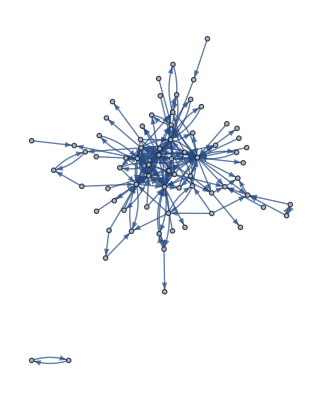

```mathematica
Graph[compOnlyEdges,VertexLabels->Placed[Automatic,Tooltip]]
```

## Finding Communities

We can see how these articles relate with CommunityGraphPlot.

```mathematica
CommunityGraphPlot[compOnlyEdges,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-

It’s important to note that this contains just 74 of the 100 articles in our set. That is because the other 26 articles neither cite nor are cited by any of the other articles in the set. We can see this from:

```mathematica
Length@Flatten@FindGraphCommunities[compOnlyEdges]
```

74

To include all articles in our set, we can add to compOnlyEdges an extra 100 edges where each edge is self-referential.

```mathematica
compOnlySingle = Union@Flatten@Append[compOnlyEdges,
	Table[Keys[compData][[i]]->Keys[compData][[i]],{i,Length[Keys[compData]]}]];
```

```mathematica
CommunityGraphPlot[compOnlySingle,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-

Now we can see all the articles, but it’s not very helpful. Instead, we can maintain a list of articles that are not cited within our 100-article set.

```mathematica
noLinks = Complement[Keys[compData],Flatten@FindGraphCommunities[compOnlyEdges]];
```

Using this,

```mathematica
CommunityGraphPlot[compOnlyEdges,VertexLabels->Placed[Automatic,Tooltip]]
```

-Graphics-

which is the same graph as that displayed at the beginning of this section but in a different layout, we can generate groups. CommunityGraphPlot takes the groupings generated by FindGraphCommunities and plots them. By running through the methods of FindGraphCommunities, we can determine that the “Modularity” model is the best.

```mathematica
CommunityGraphPlot[compOnlyEdges,
	FindGraphCommunities[
		compOnlyEdges, Method->#
	],
	VertexLabels -> Placed[Automatic, Tooltip],
	ImageSize -> Small
]&/@{
		"Modularity",
		"Centrality",
		"CliquePercolation",
		"Hierarchical",
		"Spectral",
		"VertexMoving"
	}//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Since we can generate the communities, we can go through and label them manually. The order they appear is based off of the number of articles in the list from longest to shortest.

```mathematica
groups = Association[
	Flatten[
		Map[
			Thread,
			Thread[
				FindGraphCommunities[compOnlyEdges]->
				{
					"Computational Chemistry Group",
					"Computational Science and Data Group",
					"Computational Biology Group",
					"Computational Thinking/Sentience Group",
					"Computational Intelligence and Economics Group",
					"Computational Physics Group",
					"Computational Complexity Group",
					"Computational Photography Group"
				}
			]
		]
	]
];
```

Now that we have groups assigned we can go through compOnlyEdges and replace each item with its corresponding group.

```mathematica
groupsEdges = Table[
	Replace[
		compOnlyEdges[[i]],
		compOnlyEdges[[i]] -> (
			groups[compOnlyEdges[[i]][[1]]]-> groups[compOnlyEdges[[i]][[2]]]
		)
	],
	{i,Length[compOnlyEdges]}
];
```

We can look at what this graph looks like.

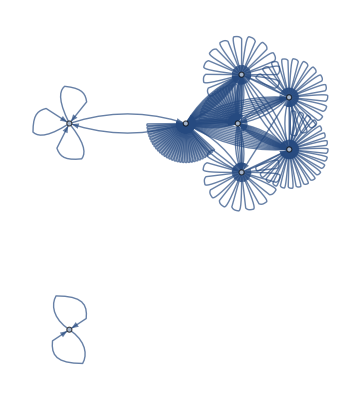

```mathematica
Graph[groupsEdges,VertexLabels->Placed[Automatic,Tooltip]]
```

As expected, a CommunityGraphPlot using FindGraphCommunities of every model yields almost identical results as everything has already been grouped previously.

```mathematica
CommunityGraphPlot[
	groupsEdges,
	FindGraphCommunities[groupsEdges,Method->#],
	VertexLabels->Placed[Automatic,Tooltip],
	ImageSize->Small
]&/@{"Modularity","Centrality","CliquePercolation","Hierarchical","Spectral"}//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

If we want to remove the self-referential loops, we use GraphPlot instead. Note the single point that is entirely self-referential, therefore not pointing in either direction to other groups.

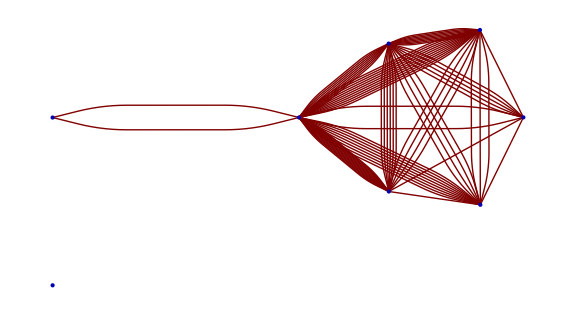

```mathematica
GraphPlot[groupsEdges,SelfLoopStyle->None,VertexLabeling->Tooltip,ImageSize->Large]
```

## Looking at Edit Histories

The site “tools.wmflabs.org” has much information about edit statistics of all articles on Wikipedia. To collect our data we take the template

```mathematica
template ={"https://tools.wmflabs.org/xtools-articleinfo/?article=","&project=en.wikipedia.org"};
```

and insert our article title in between. However, our list of articles needs to have spaces replaced by “_” before we can call the data so we must do this:

```mathematica
urlForm = Flatten @ Table[StringReplace[i, " "-> "_"], {i, Keys[compData]}];
```

This function will allow us to call the necessary information:

```mathematica
TitleToEdit[article_] := 
	Block[{}, 
		Print[template[[1]]<> article <> template[[2]]]; 
		Import[template[[1]]<> article <> template[[2]], "XML"]
	]
```